```mathematica
(*Phase Diagram Plot*)
Manipulate[Plot[r*P+beta,{P,0,20}],{r,-1,1},{beta,-3,3}]
```

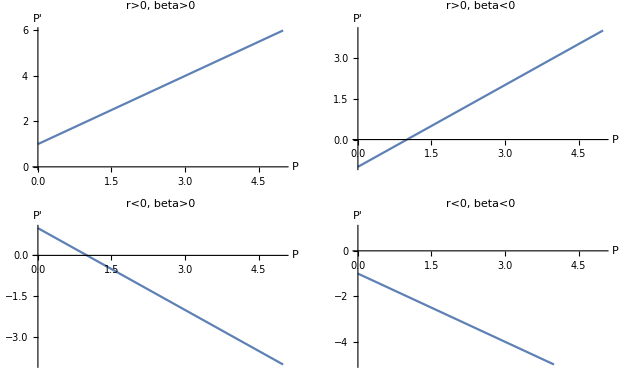

```mathematica
rr1 = 1; bbeta1 = 1; plt1 = Plot[rr1*P+bbeta1,{P,0,5},PlotRange->{0,6},AxesLabel->{P,P'},PlotLabel->"r>0, beta>0"];
rr2 = 1; bbeta2 = -1;plt2 = Plot[rr2*P+bbeta2,{P,0,5},AxesLabel->{P,P'},PlotLabel->"r>0, beta<0"];
rr3 = -1; bbeta3 = 1; plt3 = Plot[rr3*P+bbeta3,{P,0,5},AxesLabel->{P,P'},PlotLabel->"r<0, beta>0"];
rr4 = -1; bbeta4 = -1;plt4 = Plot[rr4*P+bbeta4,{P,0,5},PlotRange->{-5,1},AxesLabel->{P,P'},PlotLabel->"r<0, beta<0"];
Show[GraphicsGrid[{{plt1,plt2},{plt3,plt4}}]]
```

```mathematica
Export["C:\\dev\\git\\Math227AProject\\detModelFigs\\phaseDiagrams.png",%109,"PNG"]
```

C:\dev\git\Math227AProject\detModelFigs\phaseDiagrams.png

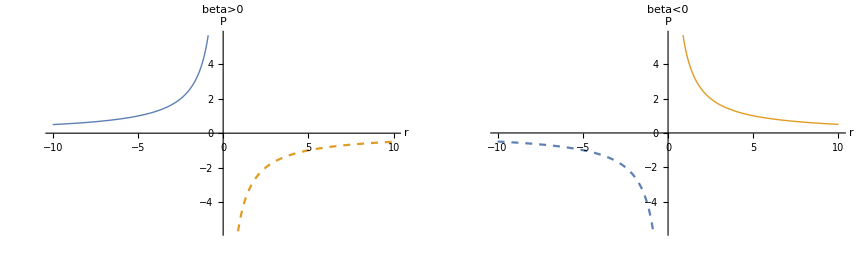

```mathematica
(*Bifurcation Plot showing what happens as we vary beta, the immigration term*)
beta1 = 5; beta2 = -5; 
ff1Neg[r_] := Piecewise[{{-beta1/r,r<0}},False]
ff1Pos[r_] := Piecewise[{{-beta1/r,r>0}},False]
ff2Neg[r_] := Piecewise[{{-beta2/r,r<0}},False]
ff2Pos[r_] := Piecewise[{{-beta2/r,r>0}},False]
plot1 = Plot[{ff1Neg[r],ff1Pos[r]},{r,-10,10},PlotStyle->{Thick,Dashed},PlotLabel->"beta>0",AxesLabel->{r,P}];
plot2 = Plot[{ff2Neg[r],ff2Pos[r]},{r,-10,10},PlotStyle->{Dashed,Thick},PlotLabel->"beta<0",AxesLabel->{r,P}];
Show[GraphicsRow[{plot1,plot2}]]
```

```mathematica
Export["C:\\dev\\git\\Math227AProject\\detModelFigs\\bifurcationPlotBeta.png",%118,"PNG"]
```

C:\dev\git\Math227AProject\detModelFigs\bifurcationPlotBeta.png

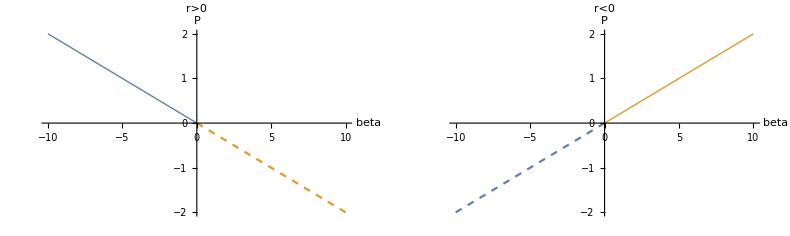

```mathematica
(*Bifurcation Plot showing what happens as we vary r, the birth-death rate*)
r1 = 5; r2 = -5; 
gg1Neg[beta_] := Piecewise[{{-beta/r1,beta<0}},False]
gg1Pos[beta_] := Piecewise[{{-beta/r1,beta>0}},False]
gg2Neg[beta_] := Piecewise[{{-beta/r2,beta<0}},False]
gg2Pos[beta_] := Piecewise[{{-beta/r2,beta>0}},False]
plotA = Plot[{gg1Neg[r],gg1Pos[r]},{r,-10,10},PlotStyle->{Thick,Dashed},PlotStyle->{Thick,Dashed},PlotLabel->"r>0",AxesLabel->{beta,P}];
plotB = Plot[{gg2Neg[r],gg2Pos[r]},{r,-10,10},PlotStyle->{Dashed,Thick},PlotStyle->{Thick,Dashed},PlotLabel->"r<0",AxesLabel->{beta,P}];
Show[GraphicsRow[{plotA,plotB}]]
```

```mathematica
Export["C:\\dev\\git\\Math227AProject\\detModelFigs\\bifurcationPlotRvalue.png",%127,"PNG"]
```

C:\dev\git\Math227AProject\detModelFigs\bifurcationPlotRvalue.png